```mathematica
ClearAll;
Density=1000.0;
Gravity=9.8;
Zin=1.0;
As=0.04*0.04;
At=1.0;
K=As*Density*Sqrt[2*Gravity]/At
```

7.0835

```mathematica
Eq1 = Z'[t] == -K*Sqrt[Z[t]];
ZZ[t_]=Z[t]/.First@FullSimplify[DSolve[{Eq1,Z[0]==Zin},Z[t],t]];
```

```mathematica
ZZ[t]
```

1.+t (-7.0835+12.544 t)

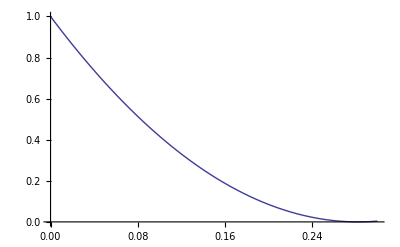

```mathematica
Plot[ZZ[t],{t,0,0.3}]
```

```mathematica
VV[t_] := Sqrt[2*Gravity*ZZ[t]];
```

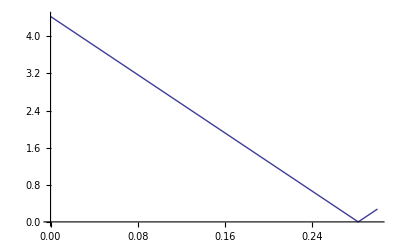

```mathematica
Plot[VV[t],{t,0,0.3}]
```